We called the regulator ϵ0.
Now we have Kruczenki’s relation between cutoffs ϵ0 = ArcTanh[ϵ].

## LerchPhi for |a|>>1

```mathematica
rulelerchasymptotics={LerchPhi[z_,s_,a_]:>Sign[a](1/(a^s (1-z))-(a^(-1-s) s z)/(1-z)^2+(a^(-2-s) s (1+s) (z+z^2))/(2 (1-z)^3)-(a^(-3-s) s (1+s) (2+s) (z+4 z^2+z^3))/(6 (1-z)^4)+(a^(-4-s) s (1+s) (2+s) (3+s) (z+11 z^2+11 z^3+z^4))/(24 (1-z)^5)-(a^(-5-s) s (1+s) (2+s) (3+s) (4+s) (z+26 z^2+66 z^3+26 z^4+z^5))/(120 (1-z)^6)+1/(720 (1-z)^7)a^(-6-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (z+57 z^2+302 z^3+302 z^4+57 z^5+z^6)-1/(5040 (1-z)^8)a^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (z+120 z^2+1191 z^3+2416 z^4+1191 z^5+120 z^6+z^7)+1/(40320 (1-z)^9)a^(-8-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (z+247 z^2+4293 z^3+15619 z^4+15619 z^5+4293 z^6+247 z^7+z^8)-1/(362880 (1-z)^10)a^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (z+502 z^2+14608 z^3+88234 z^4+156190 z^5+88234 z^6+14608 z^7+502 z^8+z^9)+1/(3628800 (1-z)^11)a^(-10-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (z+1013 z^2+47840 z^3+455192 z^4+1310354 z^5+1310354 z^6+455192 z^7+47840 z^8+1013 z^9+z^10)-1/(39916800 (1-z)^12)a^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (z+2036 z^2+152637 z^3+2203488 z^4+9738114 z^5+15724248 z^6+9738114 z^7+2203488 z^8+152637 z^9+2036 z^10+z^11)+1/(479001600 (1-z)^13)a^(-12-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (z+4083 z^2+478271 z^3+10187685 z^4+66318474 z^5+162512286 z^6+162512286 z^7+66318474 z^8+10187685 z^9+478271 z^10+4083 z^11+z^12)-1/(6227020800 (1-z)^14)a^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (z+8178 z^2+1479726 z^3+45533450 z^4+423281535 z^5+1505621508 z^6+2275172004 z^7+1505621508 z^8+423281535 z^9+45533450 z^10+1479726 z^11+8178 z^12+z^13)+1/(87178291200 (1-z)^15)a^(-14-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (z+16369 z^2+4537314 z^3+198410786 z^4+2571742175 z^5+12843262863 z^6+27971176092 z^7+27971176092 z^8+12843262863 z^9+2571742175 z^10+198410786 z^11+4537314 z^12+16369 z^13+z^14)-(a^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (z+32752 z^2+13824739 z^3+848090912 z^4+15041229521 z^5+102776998928 z^6+311387598411 z^7+447538817472 z^8+311387598411 z^9+102776998928 z^10+15041229521 z^11+848090912 z^12+13824739 z^13+32752 z^14+z^15))/(1307674368000 (1-z)^16))};
rulelerchtohyper={LerchPhi[z_,1,a_]:>1/a Hypergeometric2F1[1,a,a+1,z]};
```

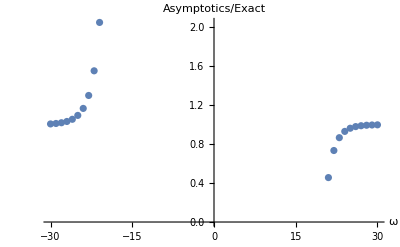

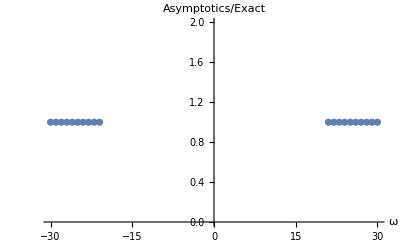

```mathematica
R=SetPrecision[RandomReal[{1,5}],40];
ϵ0=SetPrecision[RandomReal[{10^-3,0.5}],40];
σ0=SetPrecision[RandomReal[{0.5,1}],40];

tmp=LerchPhi[ⅇ^(-2 ϵ0),1,ω];
tmp=(tmp/.rulelerchasymptotics)/tmp;
ListPlot[Table[{ω,If[Abs[ω]≤20,NaN,tmp]},{ω,-30,30}],PlotRange->All,AxesLabel->{"ω","Asymptotics/Exact"}]

tmp=LerchPhi[-ⅇ^(-2 (ϵ0+σ0)),1,ω];
tmp=(tmp/.rulelerchasymptotics)/tmp;
ListPlot[Table[{ω,If[Abs[ω]≤20,NaN,tmp]},{ω,-30,30}],PlotRange->All,AxesLabel->{"ω","Asymptotics/Exact"}]

Clear[R,ϵ0,σ0]
```

## Other definitions

```mathematica
Ω[σ_]:=√Cosh[σ0] √Cosh[2 σ+σ0] Csch[σ] Sech[σ+σ0]
((√(1/Sinh[σ]^2+1/Cosh[σ+σ0]^2))/Ω[σ])^2==1//FullSimplify
```

True

## Ricci scalar

```mathematica
R2=-2/Ω[σ]^2 D[Log[Ω[σ]],{σ,2}]//TrigToExp//Together//Simplify
```

-((2 (1-ⅇ^(2 σ0)+6 ⅇ^(2 (σ+σ0))+3 ⅇ^(4 (σ+σ0))+2 ⅇ^(6 (σ+σ0))-ⅇ^(6 (2 σ+σ0))-3 ⅇ^(4 σ+2 σ0)+2 ⅇ^(6 σ+2 σ0)+3 ⅇ^(8 σ+4 σ0)-3 ⅇ^(8 σ+6 σ0)+6 ⅇ^(10 σ+6 σ0)+ⅇ^(12 σ+8 σ0)))/((1+ⅇ^(2 σ0)) (1+ⅇ^(4 σ+2 σ0))^3))

```mathematica
tmp=Integrate[Ω[σ]^2 R2,σ]//TrigToExp//Together//Simplify;
R2INT=(tmp/.σ->Log[r])-(tmp/.σ->ϵ0)//Series[#,{r,∞,0}]&//Normal;
χv=(2π)/(4π)R2INT
```

-(2 (1+3 ⅇ^(4 ϵ0+2 σ0)-ⅇ^(6 ϵ0+2 σ0)+ⅇ^(6 ϵ0+4 σ0)))/((-1+ⅇ^(2 ϵ0)) (1+ⅇ^(2 (ϵ0+σ0))) (1+ⅇ^(4 ϵ0+2 σ0)))

```mathematica
χvcir=χv/.{σ0->Log[s0]}//Series[#,{s0,∞,0}]&//Normal//ExpToTrig//FullSimplify
```

1-Coth[ϵ0]

## Full list of determinants (usual indexing, then some will shift)

```mathematica
O1[ω_]:=Piecewise[{{(ⅇ^((R-ϵ0) Abs[ω]) (Abs[ω]+Cosh[ϵ0]/Sinh[ϵ0]))/(2 Abs[ω] (1+Abs[ω])),Abs[ω]≥2},{(ⅇ^(R-ϵ0) (1+Cosh[ϵ0]/Sinh[ϵ0]))/4,ω==1},{(R Cosh[ϵ0])/Sinh[ϵ0],ω==0},{(ⅇ^(R-ϵ0) (1+Cosh[ϵ0]/Sinh[ϵ0]))/4,ω==-1}}]
O1cir[ω_]:=O1[ω]
O2[ω_]:=Piecewise[{{(ⅇ^((R-ϵ0) Abs[ω]) (Abs[ω]+Sinh[ϵ0+σ0]/Cosh[ϵ0+σ0]))/(2 Abs[ω] (1+Abs[ω])),Abs[ω]≥2},{(ⅇ^(R-ϵ0) (1+Sinh[ϵ0+σ0]/Cosh[ϵ0+σ0]))/4,ω==1},{(R Sinh[ϵ0+σ0])/Cosh[ϵ0+σ0],ω==0},{(ⅇ^(R-ϵ0) (1+Sinh[ϵ0+σ0]/Cosh[ϵ0+σ0]))/4,ω==-1}}]
O2cir[ω_]:=Piecewise[{{ⅇ^((R-ϵ0) Abs[ω])/(2 Abs[ω]),Abs[ω]≥2},{ⅇ^(R-ϵ0)/2,ω==1},{R,ω==0},{ⅇ^(R-ϵ0)/2,ω==-1}}]
O3up[ω_]:=Piecewise[{{(ⅇ^(-σ0-ϵ0 (1+ω)) ⅇ^(R(-1+ω)) (-1+ω+ⅇ^(4 ϵ0+2 σ0) (1+ω)))/(2 √(1+ⅇ^(4 ϵ0+2 σ0)) (-1+ω^2)),ω≥ 2},{(ⅇ^(2 ϵ0+σ0) R)/(√(1+ⅇ^(4 ϵ0+2 σ0))),ω==1},{(ⅇ^(ϵ0+σ0) ⅇ^R)/(2 √(1+ⅇ^(4 ϵ0+2 σ0))),ω==0},{(ⅇ^σ0 ⅇ^(2R))/(4 √(1+ⅇ^(4 ϵ0+2 σ0))),ω==-1},{(ⅇ^(ϵ0+σ0+ϵ0 ω) ⅇ^(R(1-ω)))/(√(1+ⅇ^(4 ϵ0+2 σ0)) (2-2 ω)),ω≤-2}}]
O3upcir[ω_]:=Piecewise[{{ⅇ^((R-ϵ0) (-1+ω))/(2 (-1+ω)),ω≥ 2},{R,ω==1},{ⅇ^(R-ϵ0)/2,ω==0},{1/4 ⅇ^(2 R-2 ϵ0),ω==-1},{ⅇ^(-(R-ϵ0) (-1+ω))/(2(1-ω)),ω≤-2}}]
O3down[ω_]:=O3up[-ω]
O3downcir[ω_]:=O3upcir[-ω]
```

I suspect that an imaginary unit has been missed (see checks below).

```mathematica
correction=-1;
pref=(ⅇ^(R-σ0/2) Cosh[ϵ0+σ0] Sinh[ϵ0] (1+Tanh[σ0]))/(2 √2 √Cosh[2 ϵ0+σ0]);
prefcir=1/4 ⅇ^(R-ϵ0) (-1+ⅇ^(2 ϵ0));
```

```mathematica
Ofermp56plus[ω_]:= (pref  Piecewise[{{correction ⅇ^(-2 R-σ0+2 (R-ϵ0) ω)/(4 ω^2 (1+ω) (1-ω^2)) (4 LerchPhi[ⅇ^(-2 ϵ0),1,ω] Sech[σ0] (ω+Tanh[σ0])^2+4 LerchPhi[-ⅇ^(-2 (ϵ0+σ0)),1,ω] (2 ω^2 (1-ω^2) Cosh[σ0]-Sech[σ0] (1-ω^2-Sech[σ0]^2)-2 ω (1-ω^2) Sinh[σ0])-2 ω (ω^2 Cosh[σ0]^2 Csch[ϵ0] Sech[ϵ0+σ0]-Cosh[σ0] (-2+ω+2 ω^2+2 Coth[ϵ0]+ω Coth[ϵ0]^2+3 ω^2 Cosh[2 ϵ0+σ0] Csch[ϵ0] Sech[ϵ0+σ0])+  2((1+Coth[ϵ0]) Sech[σ0]-3 ω Cosh[ϵ0] Sech[ϵ0+σ0]+(ω-2 ω Coth[ϵ0]-Csch[ϵ0]^2) Sinh[σ0]))+  (1+Coth[ϵ0]) Csch[ϵ0] Sech[ϵ0+σ0] (Cosh[2 (ϵ0+σ0)]+ⅇ^σ0 (Cosh[σ0]-Sinh[2 ϵ0-σ0]-2 Sinh[σ0])) Tanh[σ0]^2),ω≥ 2},{R ((2 (1-2 ⅇ^(2 ϵ0)+ⅇ^(4 ϵ0)+3 ⅇ^(2 σ0)-5 ⅇ^(2 (ϵ0+σ0))+ⅇ^(4 (ϵ0+σ0))+3 ⅇ^(4 ϵ0+2 σ0)+ⅇ^(2 ϵ0+4 σ0)+ⅇ^(4 ϵ0+6 σ0)))/((-1+ⅇ^(2 ϵ0))^2 (1+ⅇ^(2 σ0))^2 (1+ⅇ^(2 (ϵ0+σ0))))-(8 ⅇ^(4 σ0) σ0)/((1+ⅇ^(2 σ0))^3)-(4 ⅇ^(4 σ0) Log[-1+ⅇ^(2 ϵ0)])/((1+ⅇ^(2 σ0))^3)+(4 ⅇ^(4 σ0) Log[1+ⅇ^(2 ϵ0+2 σ0)])/((1+ⅇ^(2 σ0))^3)),ω==1},{1/((1+ⅇ^(2 σ0))^2)2 R (((1+ⅇ^(2 σ0)) (1-ⅇ^(2 ϵ0)+ⅇ^(4 ϵ0)-ⅇ^(2 σ0)+3 ⅇ^(2 (ϵ0+σ0))+ⅇ^(4 (ϵ0+σ0))))/((-1+ⅇ^(2 ϵ0))^2 (1+ⅇ^(2 (ϵ0+σ0))))-4 ⅇ^(2 σ0) σ0-2 ⅇ^(2 σ0) Log[-1+ⅇ^(2 ϵ0)]+2 ⅇ^(2 σ0) Log[1+ⅇ^(2 (ϵ0+σ0))]),ω==0},{ⅇ^(2 R) ((ⅇ^(2 ϵ0)-3 ⅇ^(2 σ0)-ⅇ^(4 σ0)+7 ⅇ^(2 (ϵ0+σ0))-2 ⅇ^(4 ϵ0+2 σ0)+2 ⅇ^(2 ϵ0+4 σ0))/(4 (-1+ⅇ^(2 ϵ0))^2 (1+ⅇ^(2 σ0)) (1+ⅇ^(2 (ϵ0+σ0))))-(ⅇ^(2 σ0) σ0)/((1+ⅇ^(2 σ0))^2)-(ⅇ^(2 σ0) Log[-1+ⅇ^(2 ϵ0)])/(2 (1+ⅇ^(2 σ0))^2)+(ⅇ^(2 σ0) Log[1+ⅇ^(2 ϵ0+2 σ0)])/(2 (1+ⅇ^(2 σ0))^2)),ω==-1},{correction ⅇ^(2 (-R+ϵ0) ω)/(4 (1-ω)^2 ω) Sech[σ0]^2 (ω+(1+ω) Cosh[2 σ0]+2 LerchPhi[ⅇ^(-2 ϵ0),1,-ω]-Cosh[ϵ0-σ0] Sech[ϵ0+σ0]+Sinh[2 σ0]+2 LerchPhi[-ⅇ^(-2 (ϵ0+σ0)),1,-ω] (-1+ω^2+ω (ω Cosh[2 σ0]+Sinh[2 σ0]))+Cosh[σ0]^2 (-2 ω Coth[ϵ0]+Csch[ϵ0]^2+4 ω Tanh[ϵ0+σ0])),ω≤- 2}}])^(1/2)
Ofermp56pluscir[ω_]:= ( prefcir Piecewise[{{-(ⅇ^(2 (R-ϵ0) (-1+ω)) (1+(-1+ⅇ^(2 ϵ0)) ω))/((-1+ⅇ^(2 ϵ0))^2 (-1+ω) ω^2)correction,ω≥ 2},{(2 ⅇ^(2 ϵ0)R)/((-1+ⅇ^(2 ϵ0))^2),ω==1},{(2 ⅇ^(2 ϵ0) R)/((-1+ⅇ^(2 ϵ0))^2),ω==0},{ (ⅇ^(2 R-2 ϵ0) (-1+2 ⅇ^(2 ϵ0)))/(4 (-1+ⅇ^(2 ϵ0))^2),ω==-1},{correction(ⅇ^(2 (-R+ϵ0) ω) (-ⅇ^(2 ϵ0) (-1+ω)+ω))/((-1+ⅇ^(2 ϵ0))^2 (-1+ω)^2 ω),ω≤- 2}}])^(1/2)
Ofermp56minus[ω_]:= Ofermp56plus[-ω]
Ofermp56minuscir[ω_]:=Ofermp56pluscir[-ω]
```

```mathematica
Ofermp56plusTable[ω_]:= (pref  Piecewise[{{correction ⅇ^(-2 R-σ0+2 (R-ϵ0) ω)/(4 ω^2 (1+ω) (1-ω^2)) (4 LerchPhiTable[ω,ϵ0] Sech[σ0] (ω+Tanh[σ0])^2+4 LerchPhiTable[ω,ϵ0,σ0] (2 ω^2 (1-ω^2) Cosh[σ0]-Sech[σ0] (1-ω^2-Sech[σ0]^2)-2 ω (1-ω^2) Sinh[σ0])-2 ω (ω^2 Cosh[σ0]^2 Csch[ϵ0] Sech[ϵ0+σ0]-Cosh[σ0] (-2+ω+2 ω^2+2 Coth[ϵ0]+ω Coth[ϵ0]^2+3 ω^2 Cosh[2 ϵ0+σ0] Csch[ϵ0] Sech[ϵ0+σ0])+  2((1+Coth[ϵ0]) Sech[σ0]-3 ω Cosh[ϵ0] Sech[ϵ0+σ0]+(ω-2 ω Coth[ϵ0]-Csch[ϵ0]^2) Sinh[σ0]))+  (1+Coth[ϵ0]) Csch[ϵ0] Sech[ϵ0+σ0] (Cosh[2 (ϵ0+σ0)]+ⅇ^σ0 (Cosh[σ0]-Sinh[2 ϵ0-σ0]-2 Sinh[σ0])) Tanh[σ0]^2),ω≥ 2},{R ((2 (1-2 ⅇ^(2 ϵ0)+ⅇ^(4 ϵ0)+3 ⅇ^(2 σ0)-5 ⅇ^(2 (ϵ0+σ0))+ⅇ^(4 (ϵ0+σ0))+3 ⅇ^(4 ϵ0+2 σ0)+ⅇ^(2 ϵ0+4 σ0)+ⅇ^(4 ϵ0+6 σ0)))/((-1+ⅇ^(2 ϵ0))^2 (1+ⅇ^(2 σ0))^2 (1+ⅇ^(2 (ϵ0+σ0))))-(8 ⅇ^(4 σ0) σ0)/((1+ⅇ^(2 σ0))^3)-(4 ⅇ^(4 σ0) Log[-1+ⅇ^(2 ϵ0)])/((1+ⅇ^(2 σ0))^3)+(4 ⅇ^(4 σ0) Log[1+ⅇ^(2 ϵ0+2 σ0)])/((1+ⅇ^(2 σ0))^3)),ω==1},{1/((1+ⅇ^(2 σ0))^2)2 R (((1+ⅇ^(2 σ0)) (1-ⅇ^(2 ϵ0)+ⅇ^(4 ϵ0)-ⅇ^(2 σ0)+3 ⅇ^(2 (ϵ0+σ0))+ⅇ^(4 (ϵ0+σ0))))/((-1+ⅇ^(2 ϵ0))^2 (1+ⅇ^(2 (ϵ0+σ0))))-4 ⅇ^(2 σ0) σ0-2 ⅇ^(2 σ0) Log[-1+ⅇ^(2 ϵ0)]+2 ⅇ^(2 σ0) Log[1+ⅇ^(2 (ϵ0+σ0))]),ω==0},{ⅇ^(2 R) ((ⅇ^(2 ϵ0)-3 ⅇ^(2 σ0)-ⅇ^(4 σ0)+7 ⅇ^(2 (ϵ0+σ0))-2 ⅇ^(4 ϵ0+2 σ0)+2 ⅇ^(2 ϵ0+4 σ0))/(4 (-1+ⅇ^(2 ϵ0))^2 (1+ⅇ^(2 σ0)) (1+ⅇ^(2 (ϵ0+σ0))))-(ⅇ^(2 σ0) σ0)/((1+ⅇ^(2 σ0))^2)-(ⅇ^(2 σ0) Log[-1+ⅇ^(2 ϵ0)])/(2 (1+ⅇ^(2 σ0))^2)+(ⅇ^(2 σ0) Log[1+ⅇ^(2 ϵ0+2 σ0)])/(2 (1+ⅇ^(2 σ0))^2)),ω==-1},{correction ⅇ^(2 (-R+ϵ0) ω)/(4 (1-ω)^2 ω) Sech[σ0]^2 (ω+(1+ω) Cosh[2 σ0]+2 LerchPhiTable[-ω,ϵ0]-Cosh[ϵ0-σ0] Sech[ϵ0+σ0]+Sinh[2 σ0]+2 LerchPhiTable[-ω,ϵ0,σ0] (-1+ω^2+ω (ω Cosh[2 σ0]+Sinh[2 σ0]))+Cosh[σ0]^2 (-2 ω Coth[ϵ0]+Csch[ϵ0]^2+4 ω Tanh[ϵ0+σ0])),ω≤- 2}}])^(1/2)
Ofermp56minusTable[ω_]:= Ofermp56plusTable[-ω]
```

## Check limits of determinants

```mathematica
tmprandom={ϵ0->SetAccuracy[RandomReal[{0,1}],100],σ0->SetAccuracy[RandomReal[{0,1}],100],R->SetAccuracy[RandomReal[{0,1}],100]};

Table[O1[ω]-O1cir[ω],{ω,-20,20}]/.σ0->Log[s0]/.{ⅇ^a_:>ⅇ^Expand[a]}//TrigToExp//Simplify//Series[#,{s0,∞,0}]&//Normal//PowerExpand//Simplify
Table[O2[ω]-O2cir[ω],{ω,-20,20}]/.σ0->Log[s0]/.{ⅇ^a_:>ⅇ^Expand[a]}//TrigToExp//Simplify//Series[#,{s0,∞,0}]&//Normal//PowerExpand//Simplify
Table[O3up[ω]-O3upcir[ω],{ω,-20,20}]/.σ0->Log[s0]/.{ⅇ^a_:>ⅇ^Expand[a]}//TrigToExp//Simplify//Series[#,{s0,∞,0}]&//Normal//PowerExpand//Simplify
Table[O3down[ω]-O3downcir[ω],{ω,-20,20}]/.σ0->Log[s0]/.{ⅇ^a_:>ⅇ^Expand[a]}//TrigToExp//Simplify//Series[#,{s0,∞,0}]&//Normal//PowerExpand//Simplify
(Table[Ofermp56plus[ω]-Ofermp56pluscir[ω],{ω,-20,20}]/.σ0->Log[s0]/.{ⅇ^a_:>ⅇ^Expand[a]}//TrigToExp//PowerExpand//Series[#,{s0,∞,0}]&//Normal)/.tmprandom//Chop
(Table[Ofermp56minus[ω]-Ofermp56minuscir[ω],{ω,-20,20}]/.σ0->Log[s0]/.{ⅇ^a_:>ⅇ^Expand[a]}//TrigToExp//PowerExpand//Series[#,{s0,∞,0}]&//Normal)/.tmprandom//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

«3 more identical outputs»

## Center O_3^up and O_3^down

```mathematica
O3upRELABELED[l_]:=O3up[l+1];
O3upcirRELABELED[l_]:=O3upcir[l+1];
O3downRELABELED[l_]:=O3down[l-1];
O3downcirRELABELED[l_]:=O3downcir[l-1];
```

```mathematica
O3upRELABELED[l]==O3downRELABELED[-l]
O3upcirRELABELED[l]==O3downcirRELABELED[-l]
```

True

True

## Relabel fermions with 1/2-integer index

```mathematica
Ofermp56plusRELABELED[s_]:=Ofermp56plus[s+1/2];
Ofermp56pluscirRELABELED[s_]:=Ofermp56pluscir[s+1/2];
Ofermp56plusTableRELABELED[s_]:=Ofermp56plusTable[s+1/2];

Ofermp56minusRELABELED[s_]:=Ofermp56minus[s-1/2];
Ofermp56minuscirRELABELED[s_]:=Ofermp56minuscir[s-1/2];
Ofermp56minusTableRELABELED[s_]:=Ofermp56minusTable[s-1/2];
```

```mathematica
Ofermp56plusRELABELED[s]==Ofermp56minusRELABELED[-s]
Ofermp56pluscirRELABELED[s]==Ofermp56minuscirRELABELED[-s]

Ofermp56plusTableRELABELED[s]==Ofermp56minusTableRELABELED[-s]
```

True

True

True

The [input] is now the label (bosons have ω=l ∈ Z and fermions ω=s ∈ Z+1/2).

## Z_(1-loop) (Appendix D [Dekel Klose])

```mathematica
tmprandom=Flatten[({{R->SetPrecision[Random[],100]}, {ϵ0->SetPrecision[Random[],100]}, {σ0->SetPrecision[Random[],100]}})];
```

The SUSY-preserving regularization (with exponential regulators) of the sum

logZ_(1-loop) = ∑_(s ∈ Z+1/2) (ω^F)_s - ∑_(l ∈ Z) (ω^B)_l

may lead to

logZ_(1-loop) = ∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l) -4 sinh^2 μ/4 ∑_(l≥0) ⅇ^(-μ (l+1/2))(ω^F)_(l+1/2) (a la’ Dekel Klose)
or to
logZ_(1-loop) = ∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l) -μ/2(ω^F)_(1/2)-μ/2∑_(l≥1) ⅇ^(-μ l)((ω^F)_(l+1/2)-(ω^F)_(l-1/2)) (a la’ sort of Kruczenski Tirziu).

The only criterion is: logZ_(1-loop) is R-independent, whereas individual sums don’t have to.

```mathematica
bosfactor[l_]:=O1[l]^(3/2)O2[l]^(3/2)O3upRELABELED[l]^(1/2)O3downRELABELED[l]^(1/2); (* = Exp[Subscript[ω^B, l∈Z]] *)
fermfactor[s_]:=(Ofermp56plusRELABELED[s]Ofermp56minusRELABELED[s])^(4/2); (* = Exp[Subscript[ω^F, s∈Z+1/2]] *)
fermfactorTable[s_]:=(Ofermp56plusTableRELABELED[s]Ofermp56minusTableRELABELED[s])^(4/2);

factor[l_]:=(√(fermfactor[l+1/2]fermfactor[l-1/2]))/bosfactor[l] (* = Exp[(Subscript[ω^F, l+1/2]+Subscript[ω^F, l-1/2])/2-Subscript[ω^B, l]] *)
factorTable[l_]:=(√(fermfactorTable[l+1/2]fermfactorTable[l-1/2]))/bosfactor[l]

bosfactorcir[l_]:=O1cir[l]^(3/2)O2cir[l]^(3/2)O3upcirRELABELED[l]^(1/2)O3downcirRELABELED[l]^(1/2);
fermfactorcir[s_]:=(Ofermp56pluscirRELABELED[s]Ofermp56minuscirRELABELED[s])^(4/2);

factorcir[l_]:=(√(fermfactorcir[l+1/2]fermfactorcir[l-1/2]))/bosfactorcir[l]
```

R disappears in the factor only for |l|≥2

```mathematica
Table[{l,(D[factor[l],R]/.tmprandom//Chop)},{l,-10,10}]//MatrixForm
Table[{l,(D[factorcir[l],R]/.tmprandom//Chop)},{l,-10,10}]//MatrixForm
```

(-10 | 0
-9 | 0
-8 | 0
-7 | 0
-6 | 0
-5 | 0
-4 | 0
-3 | 0
-2 | 0
-1 | 1.01949497889129304574965883168212480376830028315437361836488664790741972014298308471643741119155
0 | -0.9700623607371104023600768819001121780295149703964891494611674816884675507664600096550011721611705
1 | 1.01949497889129304574965883168212480376830028315437361836488664790741972014298308471643741119155
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0)

(-10 | 0
-9 | 0
-8 | 0
-7 | 0
-6 | 0
-5 | 0
-4 | 0
-3 | 0
-2 | 0
-1 | 1.004182977735341554018449581172884053087636212184768550994721991326711250381737442039279722825673
0 | -0.8818217021257763915960057217081652961659684493311369912784312888382015660552255244877901033786603
1 | 1.004182977735341554018449581172884053087636212184768550994721991326711250381737442039279722825673
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0)

Numerator denominator are even in their labels.

```mathematica
Table[bosfactor[l]/bosfactor[-l],{l,-25,25,1}]
Table[fermfactor[s]/fermfactor[-s],{s,-51/2,51/2,1}]
Table[factor[l]/factor[-l],{l,-25,25,1}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## Asymptotics of yellow summand

```mathematica
tmp=Log[(Refine[factorcir[l],Assumptions->l≥3])/.{ⅇ^a_:>ⅇ^Expand[a],√a_:>√FullSimplify[a]}//PowerExpand//Simplify]//PowerExpand//Simplify;
tmp=tmp//Series[#,{l,∞,1}]&//Normal//Simplify
```

-(-1+Coth[ϵ0])/(2 l)

```mathematica
tmp==χvcir/(2l)//Simplify
```

True

```mathematica
tmp=Log[Refine[Refine[factor[l]//TrigToExp,Assumptions->l≥3]/.rulelerchasymptotics,Assumptions->l≥3]]/.{ⅇ^a_:>ⅇ^Expand[a],√(-((2-2 (1-l)) l (1+l) (-1+(1+l)^2))/((1-l) (2+l) (1-l^2) (1-(1+l)^2)))->PowerExpand[√Simplify[-((2-2 (1-l)) l (1+l) (-1+(1+l)^2))/((1-l) (2+l) (1-l^2) (1-(1+l)^2))]]}//TrigToExp//PowerExpand;
tmp=tmp//Series[#,{l,∞,1}]&//Normal;
tmp=Log[Exp[tmp]//Simplify]//PowerExpand
```

(-1-3 ⅇ^(4 ϵ0+2 σ0)+ⅇ^(6 ϵ0+2 σ0)-ⅇ^(6 ϵ0+4 σ0))/((-1+ⅇ^(2 ϵ0)) (1+ⅇ^(2 (ϵ0+σ0))) (1+ⅇ^(4 ϵ0+2 σ0)) l)

```mathematica
tmp==χv/(2l)//Simplify
```

True

Subtracting ~1/ω term-by-term is better than subtracting ~logΛ at the end.

Sum[#, {l,-Λ,Λ}] - χ_v Log[Λ] = 
Sum[# - If[l==0,0,χ_v/(2|l|)], {l,-Λ,Λ}] + χ_vEulerGamma

```mathematica
tmp=Sum[-If[l==0,0,chivol/(2Abs[l])],{l,-Λ,Λ}]+chivol (HarmonicNumber[Λ]-Log[Λ]);
tmp=Refine[tmp,Assumptions->Λ≥2]//Simplify
```

-chivol Log[Λ]

## Attempts on the circle

∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l)  = yellowcir1+yellowcir2 = yellowcir
Not sure about right cutoff (= Λ+const) but the result is apparently untouched.

```mathematica
Clear[const]
```

```mathematica
(* terms ω=-2,-1,0,1,2 *)
```

```mathematica
yellowcir1=Sum[Log[factorcir[ω]],{ω,-2,2}]//PowerExpand//TrigToExp//Simplify//PowerExpand//FullSimplify
```

1/2 (4 R-2 Log[12]-5 Log[-1+ⅇ^(2 ϵ0)]-3 Log[1+ⅇ^(2 ϵ0)]+8 Log[-1+2 ⅇ^(2 ϵ0)]+4 Log[-2+3 ⅇ^(2 ϵ0)]-6 Log[-1+3 ⅇ^(2 ϵ0)])

```mathematica
(* terms |ω|≥3 *)
```

```mathematica
tmp=Log[(Refine[factorcir[ω],Assumptions->ω≥3])/.{ⅇ^a_:>ⅇ^Expand[a],√a_:>√FullSimplify[a]}//PowerExpand//Simplify]//PowerExpand//Simplify;
tmp=tmp/.{Log[4 ω^2+4 ω Coth[ϵ0]+Csch[ϵ0]^2]->Log[4]+Log[ω-1/2 (-1-Coth[ϵ0])]+Log[ω-1/2 (1-Coth[ϵ0])]}//PowerExpand//FullSimplify
```

-Log[4 (-1+ω)]+Log[ω]-1/2 Log[1+ω]-3/2 Log[ω+Coth[ϵ0]]+Log[-1+2 ω+Coth[ϵ0]]+Log[1+2 ω+Coth[ϵ0]]

```mathematica
yellowcir2=2Sum[tmp,{ω,3,Λ+const}]//Series[#,{Λ,∞,0}]&//PowerExpand//Simplify//Normal;
yellowcir2=yellowcir2/.{Log[(3 Λ)/2]->Log[Λ]+Log[3/2]}//Collect[#,Log[Λ],FullSimplify]&
```

Log[3/2]+(1-Coth[ϵ0]) Log[Λ]+3 Log[Gamma[3+Coth[ϵ0]]]-2 Log[Gamma[1/2 (5+Coth[ϵ0])]]-2 Log[Gamma[1/2 (7+Coth[ϵ0])]]

```mathematica
yellowcir=yellowcir1+yellowcir2//Collect[#,Log[Λ],FullSimplify]&
Clear[yellowcir1,yellowcir2]
```

(1-Coth[ϵ0]) Log[Λ]+1/2 (4 R-2 Log[8]-5 Log[-1+ⅇ^(2 ϵ0)]-3 Log[1+ⅇ^(2 ϵ0)]+8 Log[-1+2 ⅇ^(2 ϵ0)]+4 Log[-2+3 ⅇ^(2 ϵ0)]-6 Log[-1+3 ⅇ^(2 ϵ0)]+6 Log[Gamma[3+Coth[ϵ0]]]-4 Log[Gamma[1/2 (5+Coth[ϵ0])]]-4 Log[Gamma[1/2 (7+Coth[ϵ0])]])

```mathematica
χvcir Log[Λ]
```

(1-Coth[ϵ0]) Log[Λ]

-4 sinh^2 μ/4 ∑_(l≥0) ⅇ^(-μ (l+1/2))(ω^F)_(l+1/2) = bluecir1+bluecir2+bluecir3 = bluecir

```mathematica
(* terms ω=0,1 *)
```

```mathematica
bluecir1=Sum[-4 Sinh[μ/4]^2 ⅇ^(-(ω+1/2) μ)Log[fermfactorcir[ω+1/2]],{ω,0,1}]//Series[#,{μ,0,0}]&//Normal
```

0

```mathematica
(* terms ω≥2 *)
```

```mathematica
Simplify[PowerExpand[Refine[-4 Sinh[μ/4]^2 ⅇ^(-(ω+1/2) μ)Log[fermfactorcir[ω+1/2]],Assumptions->ω≥2]/.{(-1-ω)^-2->(1+ω)^-2}]/.{ⅇ^a_:>ⅇ^Expand[a]}]/.{Log[-ω+ⅇ^(2 ϵ0) (1+ω)]->Log[ⅇ^(2 ϵ0)/(-1+ⅇ^(2 ϵ0))+ ω]+Log[(-1+ⅇ^(2 ϵ0))]}
```

-8 ⅇ^(-μ (1/2+ω)) (R-ϵ0+2 R ω-2 ϵ0 ω-Log[4]-Log[ω]-2 Log[1+ω]+Log[ⅇ^(2 ϵ0)/(-1+ⅇ^(2 ϵ0))+ω]) Sinh[μ/4]^2

```mathematica
bluecir2=Sum[-8 ⅇ^(-μ (1/2+ω)) (R-ϵ0+2 R ω-2 ϵ0 ω-Log[4]) Sinh[μ/4]^2 ,{ω,2,∞}]//Series[#,{μ,0,0}]&//Normal
```

-R+ϵ0

```mathematica
bluecir3=Sinh[μ/4]^2 ⅇ^(-μ (1/2)) (8Sum[ⅇ^(-μ (ω)) Log[ω] ,{ω,2,∞}]+Sum[16 ⅇ^(-μ (ω)) Log[1+ω] ,{ω,2,∞}]-Sum[8 ⅇ^(-μ (ω)) Log[ⅇ^(2 ϵ0)/(-1+ⅇ^(2 ϵ0))+ω],{ω,2,∞}])//Series[#,{μ,0,0}]&//Normal
```

0

```mathematica
(* sum up all terms *)
```

```mathematica
bluecir=bluecir1+bluecir2+bluecir3
Clear[bluecir1,bluecir2,bluecir3]
```

-R+ϵ0

-μ/2(ω^F)_(1/2)-μ/2∑_(l≥1) ⅇ^(-μ l)((ω^F)_(l+1/2)-(ω^F)_(l-1/2)) = greencir1+greencir2+greencir3 = greencir

```mathematica
(* first term + terms ω=1,2 *)
```

```mathematica
greencir1=-μ/2 Log[fermfactorcir[1/2]]+Sum[-μ/2 ⅇ^(-ω μ)Log[fermfactorcir[ω+1/2]/fermfactorcir[ω-1/2]],{ω,1,2}]//Series[#,{μ,0,0}]&//Normal
```

0

```mathematica
(* terms ω≥2 *)
```

We implicitly check (D1,D8) Kristjansen Makeenko:
μ Sum[ⅇ^(-μ ω)Log[(m+a)/(m+b)],{m,1,∞}] = O(μ) .

```mathematica
tmp=-μ/2 ⅇ^(-ω μ)Log[Refine[fermfactorcir[ω+1/2]/fermfactorcir[ω-1/2],Assumptions->ω≥3]//Simplify];
tmp=tmp/.{(ω-ⅇ^(2 ϵ0) (1+ω))^2->(-ω+ⅇ^(2 ϵ0) (1+ω))^2}//PowerExpand//Simplify;
tmp=tmp/.{Log[-ω+ⅇ^(2 ϵ0) (1+ω)]->Log[-(-ⅇ^(2 ϵ0)/(-1+ⅇ^(2 ϵ0))- ω)]+Log[(-1+ⅇ^(2 ϵ0))]}//Simplify
```

-ⅇ^(-μ ω) μ (2 R-2 ϵ0+Log[-1+ⅇ^(2 ϵ0)]+Log[-1+ω]+Log[ω]-2 Log[1+ω]+Log[ⅇ^(2 ϵ0)/(-1+ⅇ^(2 ϵ0))+ω]-Log[1+(-1+ⅇ^(2 ϵ0)) ω])

```mathematica
greencir2=Sum[-ⅇ^(-μ ω) μ (2 R-2 ϵ0+Log[-1+ⅇ^(2 ϵ0)]),{ω,3,∞}]//Series[#,{μ,0,0}]&//Normal
greencir3=Sum[-ⅇ^(-μ ω) μ (Log[-1+ω]),{ω,3,∞}]+Sum[-ⅇ^(-μ ω) μ (Log[ω]),{ω,3,∞}]+Sum[-ⅇ^(-μ ω) μ (-2 Log[1+ω]),{ω,3,∞}]+Sum[-ⅇ^(-μ ω) μ (Log[ⅇ^(2 ϵ0)/(-1+ⅇ^(2 ϵ0))+ω]),{ω,3,∞}]+Sum[-ⅇ^(-μ ω) μ (-Log[1+(-1+ⅇ^(2 ϵ0)) ω]),{ω,3,∞}]//Series[#,{μ,0,0}]&//Normal
```

-2 R+2 ϵ0-Log[-1+ⅇ^(2 ϵ0)]

Log[-1+ⅇ^(2 ϵ0)]

```mathematica
(* sum up all terms *)
```

```mathematica
greencir=greencir1+greencir2+greencir3//FullSimplify
Clear[greencir1,greencir2,greencir3]
```

-2 R+2 ϵ0

## Attempts on the circle: yellow+green is promising

The expected result is roughly
logZ_(1-loop) = 1/2Logπ/2 + (unknown ϵ-divergences) + O(ϵ)
whereas Kruczenski’s is
logZ_(1-loop) = -1/2Log2π + (1+Log4-Logϵ)/ϵ + O(ϵ).

The reg. choice
logZ_(1-loop) = ∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l) -4 sinh^2 μ/4 ∑_(l≥0) ⅇ^(-μ (l+1/2))(ω^F)_(l+1/2) (a la’ Dekel Klose)
is rejected because R remains.

```mathematica
yellowcir+bluecir-χvcir Log[Λ]//FullSimplify
```

R+ϵ0-Log[8]-5/2 Log[-1+ⅇ^(2 ϵ0)]-3/2 Log[1+ⅇ^(2 ϵ0)]+4 Log[-1+2 ⅇ^(2 ϵ0)]+2 Log[-2+3 ⅇ^(2 ϵ0)]-3 Log[-1+3 ⅇ^(2 ϵ0)]+3 Log[Gamma[3+Coth[ϵ0]]]-2 Log[Gamma[1/2 (5+Coth[ϵ0])]]-2 Log[Gamma[1/2 (7+Coth[ϵ0])]]

The reg. choice
logZ_(1-loop) = ∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l) -μ/2(ω^F)_(1/2)-μ/2∑_(l≥1) ⅇ^(-μ l)((ω^F)_(l+1/2)-(ω^F)_(l-1/2)) (a la’ sort of Kruczenski Tirziu)
returns the Kruczenski’s wrong result for the circle, but is a good candidate for latitude/circle where the rubbish goes away.
It is noteworthy that it’s exactly Kruczenski despite a different frequency arrangement!

```mathematica
tmp=yellowcir+greencir-χvcir Log[Λ]//FullSimplify;
tmp=tmp/.{ϵ0->ArcTanh[ϵ]}//TrigToExp//FullSimplify;
tmp=tmp//Series[#,{ϵ,0,0},Assumptions->ϵ>0]&//Normal//PowerExpand//FullSimplify//ExpandAll;
tmp=tmp//Series[#,{ϵ,0,0},Assumptions->ϵ>0]&//Normal;
tmp=tmp/.{Log[16]->4Log[2]}//Collect[#,1/ϵ,FullSimplify]&
```

-1/2 Log[2 π]+(-1+Log[4]-Log[ϵ])/ϵ

## Attempts on the latitude: let’s use yellow+green

Let’s do the same
logZ_(1-loop) = ∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l) -μ/2(ω^F)_(1/2)-μ/2∑_(l≥1) ⅇ^(-μ l)((ω^F)_(l+1/2)-(ω^F)_(l-1/2)) (a la’ sort of Kruczenski Tirziu)
on the latitude as well, where it must produce a sensible result (R-divergence free, UV divergence ~ χ_v etc.), regardless of whether the finite part is right of not.

∑_(l ∈Z) ⅇ^(-μ l)(((ω^F)_(l+1/2)+(ω^F)_(l-1/2))/2-(ω^B)_l)  = yellowfunct
I assume cutoff=Λ without shift, because the circle told it’s irrelevant.

```mathematica
yellowfunctcir[Λ_]:=Sum[Log[factorcir[ω]]-If[ω==0,0,χvcir/(2Abs[ω])],{ω,-2,2}]+2Sum[Log[Refine[factorcir[ω] ⅇ^(-χv/(2ω)),Assumptions->ω≥3]],{ω,3,Λ}]+χvcir (HarmonicNumber[Λ]-Log[Λ])
```

-μ/2(ω^F)_(1/2)-μ/2∑_(l≥1) ⅇ^(-μ l)((ω^F)_(l+1/2)-(ω^F)_(l-1/2)) = greenfunct

```mathematica
greenfunctcir[cutoff_,μ_]:=-μ/2 Log[fermfactorcir[1/2]]+Sum[-μ/2 ⅇ^(-ω μ)Log[fermfactorcir[ω+1/2]/fermfactorcir[ω-1/2]],{ω,1,2}]+Sum[-μ/2 ⅇ^(-ω μ)Log[Refine[fermfactorcir[ω+1/2]/fermfactorcir[ω-1/2],Assumptions->ω≥3]],{ω,3,cutoff}]
```

## Use hypergeometric functions

```mathematica
LerchPhiTable[ω_,ϵ0_]:=Piecewise[{{-Log[1-ⅇ^(-2 ϵ0)],ω==0},{Hypergeometric2F1[1,ω,1+ω,ⅇ^(-2 ϵ0)]/ω,ω≠0}}]
LerchPhiTable[ω_,ϵ0_,σ0_]:=Piecewise[{{-Log[1+ⅇ^(-2 (ϵ0+σ0))],ω==0},{Hypergeometric2F1[1,ω,1+ω,-ⅇ^(-2 (ϵ0+σ0))]/ω,ω≠0}}]

Nϵ0=1/1000 SetAccuracy[Rationalize[RandomReal[]],∞];
Nσ0=2SetAccuracy[Rationalize[RandomReal[]],∞];

Nsub={ϵ0->Nϵ0,σ0->Nσ0,Λ->NΛ,μ->Nμ,cutoff->Ncutoff};

Table[{ω,N[LerchPhiTable[ω,Nϵ0]-LerchPhi[ⅇ^(-2 Nϵ0),1,ω],{∞,20}]},{ω,0,20}]//MatrixForm
Table[{ω,N[LerchPhiTable[ω,Nϵ0,Nσ0]-LerchPhi[-ⅇ^(-2 (Nϵ0+Nσ0)),1,ω],{∞,20}]},{ω,0,20}]//MatrixForm

Clear[Nϵ0,Nσ0,precResult,Nsub]
```

(0 | 0.
1 | 0.
2 | 0.
3 | 0.
4 | 0.
5 | 0.
6 | 0.
7 | 0.
8 | 0.
9 | 0.
10 | 0.
11 | 0.
12 | 0.
13 | 0.
14 | 0.
15 | 0.
16 | 0.
17 | 0.
18 | 0.
19 | 0.
20 | 0.)

(0 | 0.
1 | 0.
2 | 0.
3 | 0.
4 | 0.
5 | 0.
6 | 0.
7 | 0.
8 | 0.
9 | 0.
10 | 0.
11 | 0.
12 | 0.
13 | 0.
14 | 0.
15 | 0.
16 | 0.
17 | 0.
18 | 0.
19 | 0.
20 | 0.)

Get a rough estimate of how bad numerics would be compared to the exact resummation in the circular case.

```mathematica
(*Print["Relative error for the circle yellow"]
tmp1=yellowfunctcir[NΛ]/.Nsub//N[#,precResult]&;
tmp2=yellowcir-χvcir Log[NΛ]/.Nsub//N[#,precResult]&;
(tmp1-tmp2)/tmp2//N[#,precResult]&
```

```mathematica
(*Print["Relative error for the circle green"]
tmp3=greenfunctcir[Ncutoff,Nμ]/.Nsub//N[#,precResult]&;
tmp4=greencir/.Nsub//N[#,precResult]&;
(tmp3-tmp4)/tmp4//N[#,precResult]&
```

```mathematica
(*Print["This is the expected result"]
-3/2Log[Tanh[Nσ0]]//N[#,precResult]&

Print["affected by the relative error circle green+yellow"]
(tmp1-tmp2+tmp3-tmp4)/(tmp2+tmp4)//N[#,precResult]&
```

## Simplify summands of latitude/circle

Simplified version

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Summands.nb"];
```

Temporary save

```mathematica
DumpSave[NotebookDirectory[]<>"tmp.mx","Global`"];
```